```mathematica
SetDirectory[NotebookDirectory[]];
data=Sort[Import["PQ.dat"]];
data1=Sort[Import["PQ_1_1.dat"]];
data2=Sort[Import["PQ_1_2.dat"]];
data3=Sort[Import["PQ_1_3.dat"]];
Vref=12.;
ShiftData[list_,V_,Vref_]:=Table[{list[[i,1]] V/Vref,list[[i,2]](V/Vref)^2},{i,1,Length[list]}]
fshift[list_,V_,Vref_,Q_]:=Interpolation[ShiftData[list,V,Vref]][Q]
```

```mathematica
Z=20;Manipulate[Show[ListPlot[{data1,data2,data3,ShiftData[data2,V0,12]},PlotRange->{{0,1.2},{0,40}},Joined->True,AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [m^3/min]","Pressure drop [Pa]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotLegends->Placed[{"7V","12V","13.8V",StringJoin[ToString[V0],"V"],"Operating curve"},Scaled[{0.6,0.8}]],PlotStyle->{{Blue},{Red},{Darker[Green]},{Magenta,DotDashed},{Black,Dashed}}](*,Plot[Z Q^2,{Q,0,2},PlotStyle->{Black,Dashed}]*)],{{V0,12},7,13.8}]
```

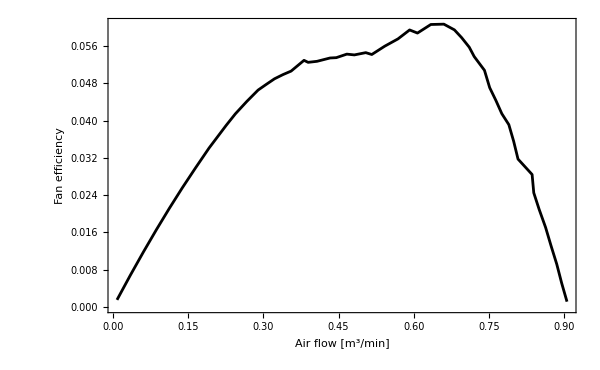

```mathematica
Power2=Table[{data2[[i,1]],data2[[i,1]] data2[[i,2]]/60 1/(12. 0.2)},{i,1,Length[data2]}];
ListPlot[Power2,PlotRange->{{data2[[1,1]],data2[[-1,1]]},All},Joined->True,Frame->True,PlotStyle->Black,AspectRatio->1/GoldenRatio,ImageSize->600,FrameLabel->{"Air flow [m^3/min]","Fan efficiency"},FrameStyle->Directive[Black,18]]
```

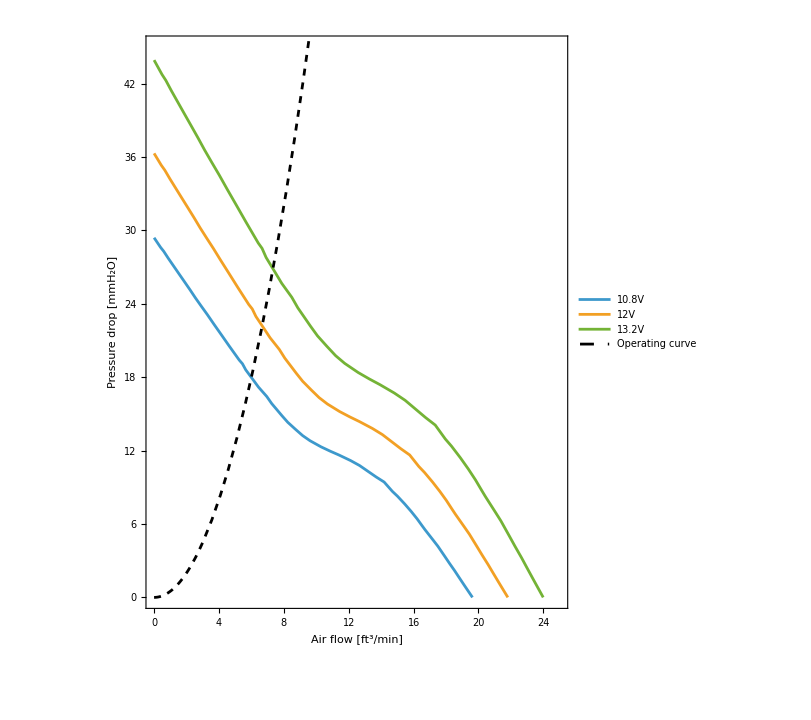

```mathematica
Z=0.5;Show[ListPlot[{ShiftData[data,10.8,Vref],data,ShiftData[data,13.2,Vref]},PlotRange->{{0,25},{0,45}},Joined->True,AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Pressure drop [mmH_2O]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotLegends->Placed[{"10.8V","12V","13.2V"},Scaled[{0.6,0.8}]]],Plot[{Z Q^2},{Q,0,25},PlotStyle->{Black,Dashed},PlotLegends->Placed[{"Operating curve"},Scaled[{0.82,0.8}]]]]
```

```mathematica
Z=0.5;Manipulate[Plot[{fshift[data,10.8,Vref,Q],fshift[data,12.,Vref,Q],fshift[data,13.2,Vref,Q],fshift[data,V0,Vref,Q],Z Q^2},{Q,0,25},PlotRange->{{0,25},{0,45}},AspectRatio->1.2,Frame->True,FrameLabel->{"Air flow [ft^3/min]","Pressure drop [mmH_2O]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotLegends->Placed[{"10.8V","12V","13.2V",StringJoin[ToString[V0],"V"],"Operating curve"},Scaled[{0.6,0.8}]],PlotStyle->{{Blue},{Red},{Darker[Green]},{Magenta,DotDashed},{Black,Dashed}}],{V0,1,20}]
```

```mathematica
QV[V_,Vref_]:=Q/.FindRoot[fshift[V,Vref,Q]-Z Q^2,{Q,5}]
```

```mathematica
Z QV[12,12]^3 0.00047194745 9.80665
```

0.683886

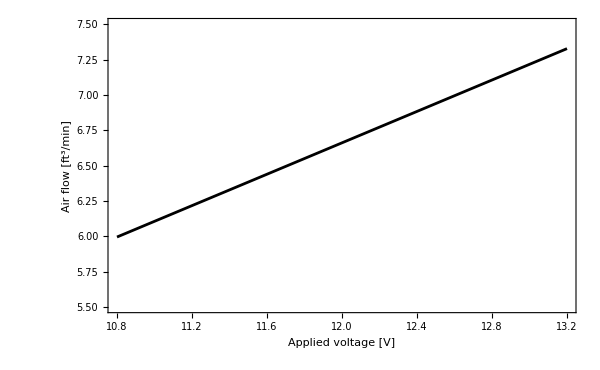

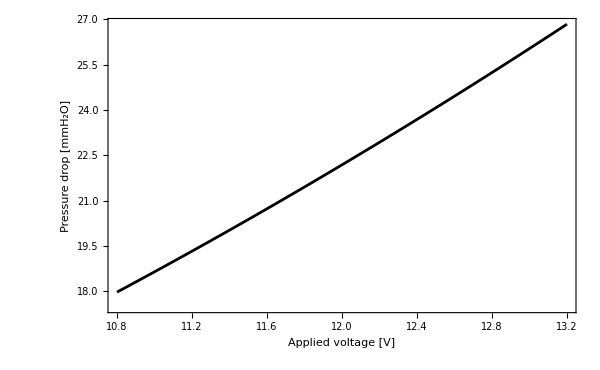

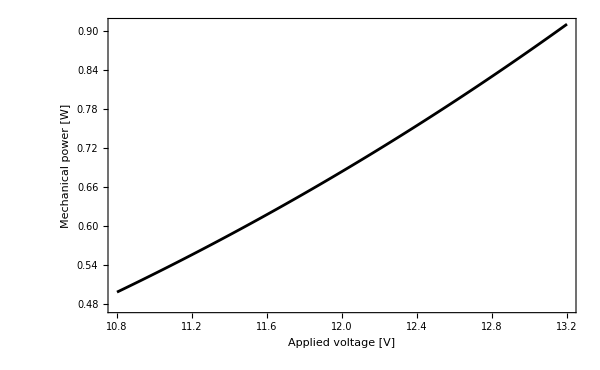

```mathematica
tQV=Table[{V,QV[V,Vref]},{V,10.8,13.2,0.01}];
ListPlot[tQV,PlotRange->{{10.8,13.2},{5.5,7.5}},Joined->True,AspectRatio->1/GoldenRatio,Frame->True,FrameLabel->{"Applied voltage [V]","Air flow [ft^3/min]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotStyle->{Black}]
tPV=Table[{V,Z QV[V,Vref]^2},{V,10.8,13.2,0.01}];
ListPlot[tPV,PlotRange->{{10.8,13.2},All},Joined->True,AspectRatio->1/GoldenRatio,Frame->True,FrameLabel->{"Applied voltage [V]","Pressure drop [mmH_2O]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotStyle->{Black}]
tpowerV=Table[{V,Z QV[V,Vref]^3 0.00047194745 9.80665},{V,10.8,13.2,0.01}];
ListPlot[tpowerV,PlotRange->{{10.8,13.2},All},Joined->True,AspectRatio->1/GoldenRatio,Frame->True,FrameLabel->{"Applied voltage [V]","Mechanical power [W]"},FrameStyle->Directive[Black,18],ImageSize->600,PlotStyle->{Black}]
```